## Beams

### Exercise 5.C1

The strategy here is to solve the reactions, then solve the shear force and bending moment in each region of the beam.
We will restrict ourselves to vertical forces and assume that the reactions only occur in the vertical direction.

Consider the general case (with these assumptions):
-Graphics-

To do this, we need equations to solve the areas of the shapes we may need. We will begin with just triangles, rectangles, and trapezoids.

```mathematica
triangleArea[len_,height_]:=1/2*len*height
rectangleArea[len_,height_]:=len*height
trapezoidArea[len_,heightA_,heightB_]:=len*((heightA+heightB)/2)
```

Now we need to calculate the reactions two supports. We only need to keep track of the location in this case (since we assume a vertical direction and we assume everything is acting in the same line of the center of the beam).

As an example:

```mathematica
forceList5C1General={
{"A reaction",aMag,0},
{"B reaction",bMag,lenBeam},
{"Distributed force 1",triangleArea[len1, height1], centroid}
};

reactionPiece[mag_,loc_,x_]:=Piecewise[
{{0,x<loc},
{mag,x≥ loc}}
]

simpleForceDist[distA_,distB_,heightA_,heightB_,x_]:=Piecewise[{{0,0*distA<x<distA},{0,x>distB},{((heightB-heightA)/(distB-distA))(x-distA)+heightA,distA<x<distB},{0,x==0}}]
simpleForceDist[dA,dB,ha,hb,x]
```

Piecewise[{{0, 0<x<dA||x>dB}, {ha+((-ha+hb) (-dA+x))/(-dA+dB), dA<x<dB}, {0, True}}]

From there we can invoke equilibrium and calculate the sum of the forces in the y and the moment about A. Now with the reactions, we write the force distributions as piecewise equations. We integrate once to get the shear force and twice to get the bending moment:

(dV(x))/dx=q(x)     and    (dM(x))/dx=V(x) 

We consider the following problem:

```mathematica
Clear[aMag,bMag]
forceList5C1={
{"A reaction",aMag,Quantity[0.2,"Meters"]},
{"B reaction",bMag,Quantity[0.7, "Meters"]},
{"Grav Gripper",Quantity[71,"Kilograms"]*Quantity[-9.8,("Newtons")/("Kilograms")],Quantity[3.7,"Meters"]},
{"SelfWeight force 1",rectangleArea[Quantity[0.2, "Meters"], Quantity[-9*9.8,"Newtons"/"Meters"]], Quantity[0.1, "Meters"]},
{"SelfWeight force 2",rectangleArea[Quantity[0.5, "Meters"], Quantity[-9*9.8,"Newtons"/"Meters"]],Quantity[0.2+0.25, "Meters"]},
{"SelfWeight force 3",rectangleArea[Quantity[3, "Meters"], Quantity[-9*9.8,"Newtons"/"Meters"]], Quantity[1.5+0.7, "Meters"]}
};
Grid[Prepend[forceList5C1,{"Name","Force","Distance to Centroid"}],Frame->All]
forceNet5C1=Sum[forceList5C1[[i]][[2]],{i,1,Length[forceList5C1]}]
momentNet5C1=Sum[forceList5C1[[i]][[3]]*forceList5C1[[i]][[2]],{i,1,Length[forceList5C1]}]
reactions5C1=Flatten[{aMag,bMag}/.
Solve[forceNet5C1==0&&momentNet5C1==0,{aMag,bMag}]];
aMag=reactions5C1[[1]]
bMag=reactions5C1[[2]]
Grid[Prepend[forceList5C1,{"Name","Force","Distance to Centroid"}],Frame->All];
Grid[Prepend[Table[{forceList5C1[[i]][[1]],forceList5C1[[i]][[2]],forceList5C1[[i]][[3]],forceList5C1[[i]][[3]]*forceList5C1[[i]][[2]]},{i,1,Length[forceList5C1]}],{"Name","Force","Distance to Centroid","Moment"}],Frame->All]
```

Name | Force | Distance to Centroid
A reaction | aMag | 0.2 m
B reaction | bMag | 0.7 m
Grav Gripper | -695.8 N | 3.7 m
SelfWeight force 1 | -17.64 N | 0.1 m
SelfWeight force 2 | -44.1 N | 0.45 m
SelfWeight force 3 | -264.6 N | 2.2 m

aMag+bMag+-1022.14 N

-3178.19 m N+aMag (0.2 m)+bMag (0.7 m)

-4925.38 N

5947.52 N

Name | Force | Distance to Centroid | Moment
A reaction | -4925.38 N | 0.2 m | -985.076 m N
B reaction | 5947.52 N | 0.7 m | 4163.27 m N
Grav Gripper | -695.8 N | 3.7 m | -2574.46 m N
SelfWeight force 1 | -17.64 N | 0.1 m | -1.764 m N
SelfWeight force 2 | -44.1 N | 0.45 m | -19.845 m N
SelfWeight force 3 | -264.6 N | 2.2 m | -582.12 m N

We now express the force distributions as functions using:

simpleForceDist[distA_,distB_,lenBeam_,heightA_,heightB_,x_]
and
reactionPiece[mag_,loc_,x_]

```mathematica
Clear[q1,q2,q3,shear,simplef]
lenBeam5=Quantity[3.7,"Meters"];
q1[x_]:=simpleForceDist[Quantity[0,"Feet"],Quantity[3,"Feet"],Quantity[0,"Pounds"/"Feet"],Quantity[300,"Pounds"/"Feet"],Quantity[x,"Feet"]]
q2[x_]:=simpleForceDist[Quantity[3,"Feet"],Quantity[5,"Feet"],Quantity[300,"Pounds"/"Feet"],Quantity[300,"Pounds"/"Feet"],Quantity[x,"Feet"]]
q3[x_]:=simpleForceDist[Quantity[5,"Feet"],lenBeam5,Quantity[400,"Pounds"/"Feet"],Quantity[400,"Pounds"/"Feet"],Quantity[x,"Feet"]]
q1[x]
q2[x]
q3[x]
(*shear[x_]:=Integrate[q1[s]+q2[s]+q3[s],{s,0,10}]
Plot[shear[x],{x,0,11}]*)
```

Piecewise[{{0, x ft>3 ft}, {100 x lb/ft, 0 ft<x ft<3 ft}, {0, True}}]

Piecewise[{{0, 0 ft<x ft<3 ft||x ft>5 ft}, {300 lb/ft, 3 ft<x ft<5 ft}, {0, True}}]

Piecewise[{{0, 0 ft<x ft<5 ft||x ft>3.7 m}, {400. lb/ft, 5 ft<x ft<3.7 m}, {0, True}}]

We can also do this with unit-less quantities.

```mathematica
Clear[ayu,byu,shearU]
(*
triangleArea[len_,height_]
rectangleArea[len_,height_]
trapezoidArea[len_,heightA_,heightB_]
simpleForceDist[distA_,distB_,heightA_,heightB_,x_]
*)

lenBeamDimLess=3.7;
q1u[x_]:=simpleForceDist[0,3.7,9*9.8,9*9.8,x]
(*q2u[x_]:=simpleForceDist[3,5,300,300,x]
q3u[x_]:=simpleForceDist[5,10,400,400,x]*)
aMagu=aMag/Quantity[1,"Newtons"];
bMagu=bMag/Quantity[1,"Newtons"];
gripMagu=-71*9.8;
ayu[x_]:=reactionPiece[aMagu,0.2,x]
byu[x_]:=reactionPiece[bMagu,0.7,x]
gyu[x_]:=reactionPiece[gripMagu,3.7,x]

q1u[x]
(*q2u[x];
q3u[x];*)
ayu[x]
byu[x]
gyu[x]
```

Piecewise[{{0, x>3.7}, {88.2, 0<x<3.7}, {0, True}}]

Piecewise[{{0, x<0.2}, {-4925.38, x≥0.2}, {0, True}}]

Piecewise[{{0, x<0.7}, {5947.52, x≥0.7}, {0, True}}]

Piecewise[{{0, x<3.7}, {-695.8, x≥3.7}, {0, True}}]

(Piecewise[{{-326.34, x>3.7}, {-88.2 x, 0.<x≤3.7}, {0., True}}])+(Piecewise[{{0, x<0.2}, {-4925.38, x≥0.2}, {0, True}}])+(Piecewise[{{0, x<0.7}, {5947.52, x≥0.7}, {0, True}}])+(Piecewise[{{0, x<3.7}, {-695.8, x≥3.7}, {0, True}}])

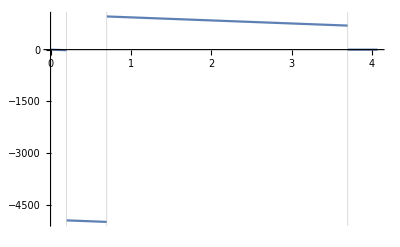

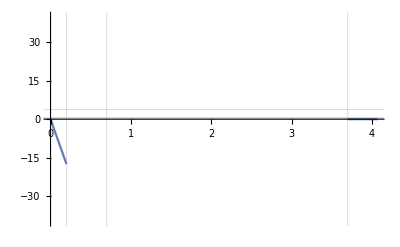

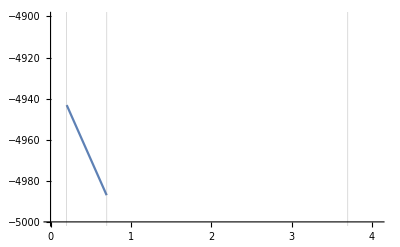

Piecewise[{{-44.1 x^2, 0.<x≤0.2}, {-0.0588 (-16753.+83765. x+750. x^2), 0.2<x≤0.7}, {-0.049 (64861.-20860. x+900. x^2), 0.7<x≤3.7}, {0., True}}]

-1.764

-2484.3

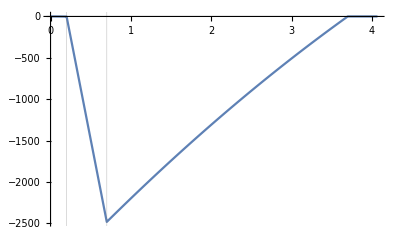

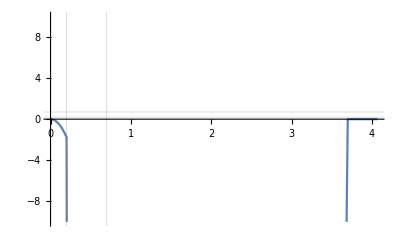

```mathematica
shearU[x_]:=ayu[x]+Integrate[-q1u[s],{s,0,x},Assumptions->x ∈ Reals]+byu[x]+gyu[x]
(*shearU[x_]:=ayu[x]+Integrate[q1u[s]+q2u[s]+q3u[s],{s,0,x},Assumptions->x ∈ Reals]+byu[x]*)

(*shearU[x_]:=Integrate[q1u[s]+q2u[s]+q3u[s],{s,0,x},Assumptions->x ∈ Reals]*)
shearU[x]
Plot[shearU[x],{x,0,lenBeamDimLess*1.1},GridLines->{{0.2, 0.7,lenBeamDimLess}},PlotRange->All]
Plot[shearU[x],{x,0,lenBeamDimLess*1.1},GridLines->{{0.2, 0.7,lenBeamDimLess}},PlotRange->{-40,40}]
Plot[shearU[x],{x,0,lenBeamDimLess*1.1},GridLines->{{0.2, 0.7,lenBeamDimLess}},PlotRange->{-5000,-4900}]
bendingU[x_]:=Integrate[shearU[s2],{s2,0,x},Assumptions->x ∈ Reals]
bendingU[x]
bendingU[0.2]
bendingU[0.7]
Plot[bendingU[x],{x,0,lenBeamDimLess*1.1},GridLines->{{0.2, 0.7}}]
Plot[bendingU[x],{x,0,lenBeamDimLess*1.1},GridLines->{{0.2, 0.7}},PlotRange->{-10,10}]
```

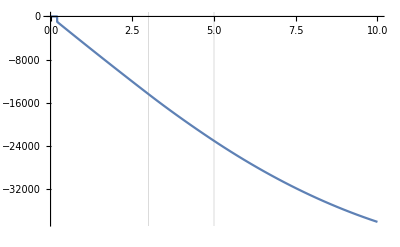

```mathematica
bendingU2[x_]:=x*ayu[x]+Integrate[Integrate[q1u[s],{s,0,s2},Assumptions->s2 ∈ Reals],{s2,0,x}, Assumptions->x ∈ Reals]+Integrate[Integrate[q2u[s],{s,0,s2},Assumptions->s2 ∈ Reals],{s2,0,x}, Assumptions->x ∈ Reals]+Integrate[Integrate[q3u[s],{s,0,s2},Assumptions->s2 ∈ Reals],{s2,0,x}, Assumptions->x ∈ Reals]
Plot[bendingU2[x],{x,0,10},GridLines->{{3, 5}}]
```

```mathematica
matA={
{1,1,450+600+2000},
{0,10 ,900+2400+15000}
}
matA //MatrixForm
RowReduce[matA]//MatrixForm
```

{{1,1,3050},{0,10,18300}}

(1 | 1 | 3050
0 | 10 | 18300)

(1 | 0 | 1220
0 | 1 | 1830)